# Introducción a la computación

## Inicialización

```mathematica
Needs["PL0Compiler`",FileNameJoin[{NotebookDirectory[],"Packages","Compiler.wl"}]];
?PL0Compiler`*
```

```mathematica
Needs["CPU`",FileNameJoin[{NotebookDirectory[],"Packages","CPU.wl"}]];
?CPU`*
```

## Introducción

Hoy en día con la ubicuidad de los celulares y computadoras rara vez nos preguntamos en qué consiste la magia de dichos dispositivos. La tecnología se ha adaptado tanto a nuestros cuerpos y nuestras mentes que por primera vez comenzamos a imaginar que nuestros aparatos electrónicos quizás algún día tengan inteligencia si es que no la tienen ya. El hecho de que podamos imaginar un posible futuro lleno de máquinas pensantes sugiere que podemos dotar de inteligencia a una máquina inorgánica modelable a partir de algoritmos y circuitos. ¿Y qué hay de la consciencia? ¿Es posible crear consciencia a partir de una IA? ¿Puede una máquina sentir? 

Antes de comenzar a tratar esas preguntas merece la pena revisar los conceptos subyacentes, ya que imaginar una consciencia inteligente en nuestros dispositivos de cómputo implica también que estos dipositivos poseen los bloques básicos sobre los cuales se podría construir una inteligencia o ser consciente.

En esencia computar consiste en usar la materia para razonar sobre algo. Durante los millones de años de evolución animal la inteligencia se ha ido refinando desde simples mecanismos de respuesta para asegurar la supervivencia hasta complejos sistemas emocionales y de representación de conocimiento que caracterizan a los mamíferos. El caso del homo sapiens es notable debido a que además de los propios sistemas de procesamiento cerebrales, somos capaces de utilizar el mundo exterior para razonar sobre el propio mundo exterior. Un ejemplo lo encontramos en el hueso de Ishango, el primer registro que se tiene sobre el uso de una herramienta externa para contar y cuya antiguiedad se estima en más de 20,000 años.

Refinamientos de civilizaciones posteriores hicieron más práctico el uso de dispositivos externos para el razonamiento numérico, como por ejemplo el desarrollo del ábaco.

Vale la pena detenerse a apreciar lo que estos dispositivos representan. Si olvidamos por un momento la facilidad en la que los dispositivos de hoy hacen cualquier operación algebraica resulta sorprendente la noción de poder moldear máquinas que extiendan nuestro pensamiento. Incluso algo tan simple como un ábaco es una hazaña biológica, es un aparato que captura parte de nuestra concepción del mundo (el concepto de número) y permite razonar sobre este a partir de movimientos de sus piezas para al final poder comprender algo nuevo. Ninguna otra especie en la tierra hace algo similar.

En la era moderna hemos sido testigos de refinaciones incluso mayores. En el pasado manejar un ábaco o contar con un hueso requería de que un humano ejecutara manualmente los movimientos necesarios para el cómputo de la operación que deseara realizar. Las máquinas de hoy en día hacen estos movimientos automaticamente sin necesidad de intervención humana. ¿Cómo logran esta autonomía? A partir de la acción ordenada de fuerzas mécanicas, hidráulicas o eléctricas. Estos dispositivos se pueden entender como cristalizaciones materiales de nuestra propia psicología; es la manera en la que imprimimos nuestro pensamiento matemático en la materia fisica. Las primeras computadoras del mundo fueron de hecho creadas con el único objetivo de realizar operaciones matemáticas con fines militares ya que la velocidad de cómputo necesaria para calcular trayectorias de proyectiles era más que la disponible en la propia mente humana, que es irónicamente la creadora de los mismos cálculos. Ejemplos hay varios, desde la máquina diferencial de Baggage (véase figura) hasta ENIAC, proyecto del ejercito estadounidense.

-Graphics-

En la actualidad el uso de máquinas mecánicas o hidráulicas para realizar cómputo ha caído en desuso, aunque aún se encuentra en dispositivos como cajas de cambios de vehículos automáticos. Éstas utilizan vías hidráulicas que regulan el estado del dispositivo por medio de la presión.

Hoy en dia contamos con dispositivos electrónicos programables capaces de ejecutar cualquier rutina, esto es, que tienen capacidades de computación universa y funcionan por medio de la manipulación de señales eléctricas dentro de los circuitos, las cuales representan operaciones lógicas o matemáticas. Un programa es una sucesión de transformaciones de señales eléctricas que se van dando dentro del CPU que es núcleo de una computadora.

## El concepto de número

Antes de continuar detengámonos a reflexionar un poco acerca del concepto de número. Después de todo si uno quiere crear máquinas que trabajen haciendo operaciones matemáticas es necesario incluir en su diseño nuestras nociones conceptuales acerca cómo se comportan estos objetos de la imaginación humana. ¿Qué representa después de todo nuestra noción del tres?

Si el lector no está muy familiarizado con las matemáticas es posible que todo intento de descripción caiga en una definición circular. E.g.: El tres es algo que tiene tres cosas. De hecho la definición de un número no es algo trivial, los matemáticos han pasado décadas definiendo reglas fundamentales sobre las cuales se puedan construir todas las demás operaciones matemáticas. En la actualidad el conjunto de axiomas de Zermelo-Fraenkel constituyen una base muy comunmente usada para definir las matemáticas.

Es algo sorprendente que durante la mayor parte de la historia escrita humana muchas civilizaciones han hecho uso de los números para diversas tareas de conteo de manera intuitiva, y no fue hasta finales de siglo XIX que se abordó por primera vez la cuestión de definir un conjunto de reglas básicas (axiomas) que den sustento a qué se puede hacer o no hacer con un número.

Los axiomas representan operaciones básicas sobre conjuntos que representan nuestras nociones de cómo se debe de comportar un conjunto. Los números se pueden definir como la cardinalidad de dichos conjuntos (la cantidad de elementos) y las operaciones matemáticas se reducen a aplicaciones de los teoremas fundamentales, los cuales se pueden manipular por medio de operaciones de lógica de primer orden.
Uno podría pensar, ¿por qué los matemáticos pierden el tiempo desarrolando una teoría matemática tan fundamental? Parece algo totalmente desconectado de la realidad y sin aplicaciones reales, pero el hecho de tener un fundamento axiomático para el concepto de número nos permite razonar lógicamente sobre los aspectos más finos de otros problemas matemáticos más aplicados. En analogía, si uno desea construir una máquina capaz de hacer operaciones matemáticas, hemos de dotarla de un conjunto de reglas que reproduzcan el comportamiento que esperamos de un número. Estas reglas no están escritas en el lenguaje de la lógica de primer orden, sino en la lógica binaria que usa unos y ceros para realizar operaciones que circuitos electrónicos pueden simular facilmente.

## Lógica binaria

La lógica binaria trabaja con variables binarias y el álgebra de boole, esto es variables que pueden tomar dos valores discretos: verdadero o falso los cuales en un circuito electrónico se pueden representar como un 1 (cable por el que pasa corriente) que representa a verdadero y un 0 (cable por el que no pasa corriente) que representa a falso. El hecho de que una variable binaria sólo pueda tener sólo dos valores puede parecer a primera vista como una desventaja, pero esto no es ninguna limitación ya que es posible combinar variables binarias para formar más números.

### Números binarios

### Representación binaria

### Código de demostración

```mathematica
comp[u_]:=Module[{v,a,b,c},v=(Append[u,0]//.  {{a___,1,0,c___}:>{a,2,"+",c},{a___,1,b_,"+",c___}:>{a,b+1,"+",c},{a___,0,c___}:>{a,1,"+",c}});
StringJoin[ToString /@ Drop[v,-1]]]

DynamicModule[{b},
Manipulate[
Text@Grid[
Join[{{" n ","binary\nnumber","subset","composition"}},
Table[
b=IntegerDigits[n,2,d];
{n,FromDigits[b],Flatten[Position[b,1]],comp[b]}
,
{n,0,2^d-1}
]
],
Background->{None,{LightOrange,{White,Lighter[Blend[{Red,Green}],.5]}}},Dividers->{{Gray,Gray,Gray,Gray},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},
Alignment->Center,
ItemSize->{{3,6,12,13}},
Frame->Black,
Spacings->{Automatic,.9}
]
,
{{d,4,"range size"},Range[8],SetterBar},ContentSize->{505,450},SaveDefinitions->True,TrackedSymbols->True
]
]
```

Fuente:
Jaime Rangel-Mondragon
“Binary Numbers, Subsets and Compositions”
http://demonstrations.wolfram.com/BinaryNumbersSubsetsAndCompositions/
Wolfram Demonstrations Project
Published: March 7 2011

### Operaciones lógicas

```mathematica
VisualizeGate[BitAnd]
```

Fuente:
Keshav Saharia
http://web.archive.org/web/20140206173429/http://keshavsaharia.com/2011/05/29/lego-logic

## Aritmética a partir de operaciones lógicas

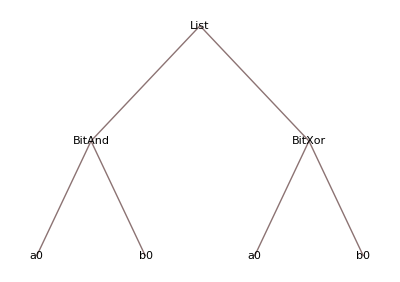

```mathematica
TreeForm[HalfAdder[a0,b0]]
```

```mathematica
PlotCompactInteractiveSystem[HalfAdder[a0,b0],ImageSize->Small]
```

```mathematica
VisualizeAdder[HalfAdder,2,"Carry"]
```

A | B | Carry | Result
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0

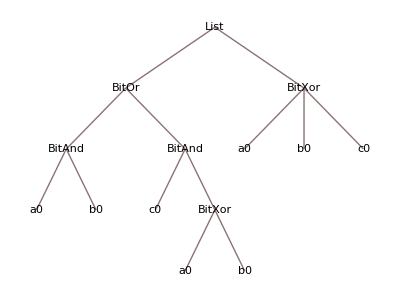

```mathematica
TreeForm[FullAdder[a0,b0,c0]]
```

```mathematica
PlotCompactInteractiveSystem[FullAdder[a0,b0,c0],ImageSize->Small]
```

```mathematica
VisualizeAdder[FullAdder,3,"Carry"]
```

A | B | C | Carry | Result
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1

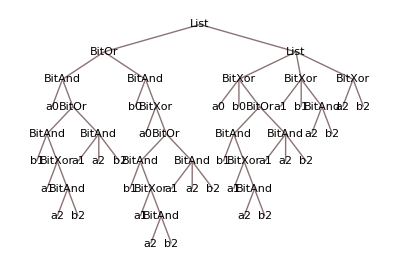

```mathematica
TreeForm[ALUAdder[{a0,a1,a2},{b0,b1,b2}]]
```

```mathematica
PlotCompactInteractiveSystem[ALUAdder[{a1,a2,a3},{b1,b2,b3}]]
```

## Un sólo circuito que hace muchas operaciones

```mathematica
PlotCompactInteractiveSystem[Mux2to1[{s},{i1,i2}],ImageSize->200]
```

```mathematica
PlotCompactInteractiveSystem[Mux4to1[{s1,s2},{i1,i2,i3,i4}]]
```

```mathematica
PlotCompactInteractiveSystem[
Values[ALUExecute[{o1,o2,o3},{a1,a2},{b1,b2}]],
EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->0.01}],
ImageSize->800,
VertexSize->0.6,
"ShowLabels"->None
]
```

## Computadora completa

```mathematica
asm = "
SetA 0
Store <n>
LoadA <n>
SetB 10
Substract
JumpZero <L$1>
Print <n>
LoadA <n>
SetB 1
Add
Store $0
SetA $0
Store <n>
Label <L$1>
Return
Declare <n> 0
";
ExecuteCodeInteractive[code,50]
```

## Un lenguaje para comunicarnos con la computadora a un nivel humano

```mathematica
program =
"procedure primes;
var arg;
begin
    arg := 2;
    while odd arg do
    begin
       arg := arg + 1
    end
end;

call primes.";
Lint[program]
```

procedure primes;
var arg;
begin
    arg := 2;
    while odd arg do
    begin
       arg := arg + 1
    end
end;

call primes.

```mathematica
tokens = Tokenize[program]
```

{<|Type→Procedure,Value→procedure|>,<|Type→Identifier,Value→primes|>,<|Type→Semicolon,Value→;|>,<|Type→Var,Value→var|>,<|Type→Identifier,Value→arg|>,<|Type→Semicolon,Value→;|>,<|Type→Begin,Value→begin|>,<|Type→Identifier,Value→arg|>,<|Type→Assign,Value→:=|>,<|Type→NumberLiteral,Value→2|>,<|Type→Semicolon,Value→;|>,<|Type→While,Value→while|>,<|Type→Odd,Value→odd|>,<|Type→Identifier,Value→arg|>,<|Type→Do,Value→do|>,<|Type→Begin,Value→begin|>,<|Type→Identifier,Value→arg|>,<|Type→Assign,Value→:=|>,<|Type→Identifier,Value→arg|>,<|Type→Plus,Value→+|>,<|Type→NumberLiteral,Value→1|>,<|Type→End,Value→end|>,<|Type→End,Value→end|>,<|Type→Semicolon,Value→;|>,<|Type→Call,Value→call|>,<|Type→Identifier,Value→primes|>,<|Type→Dot,Value→.|>}

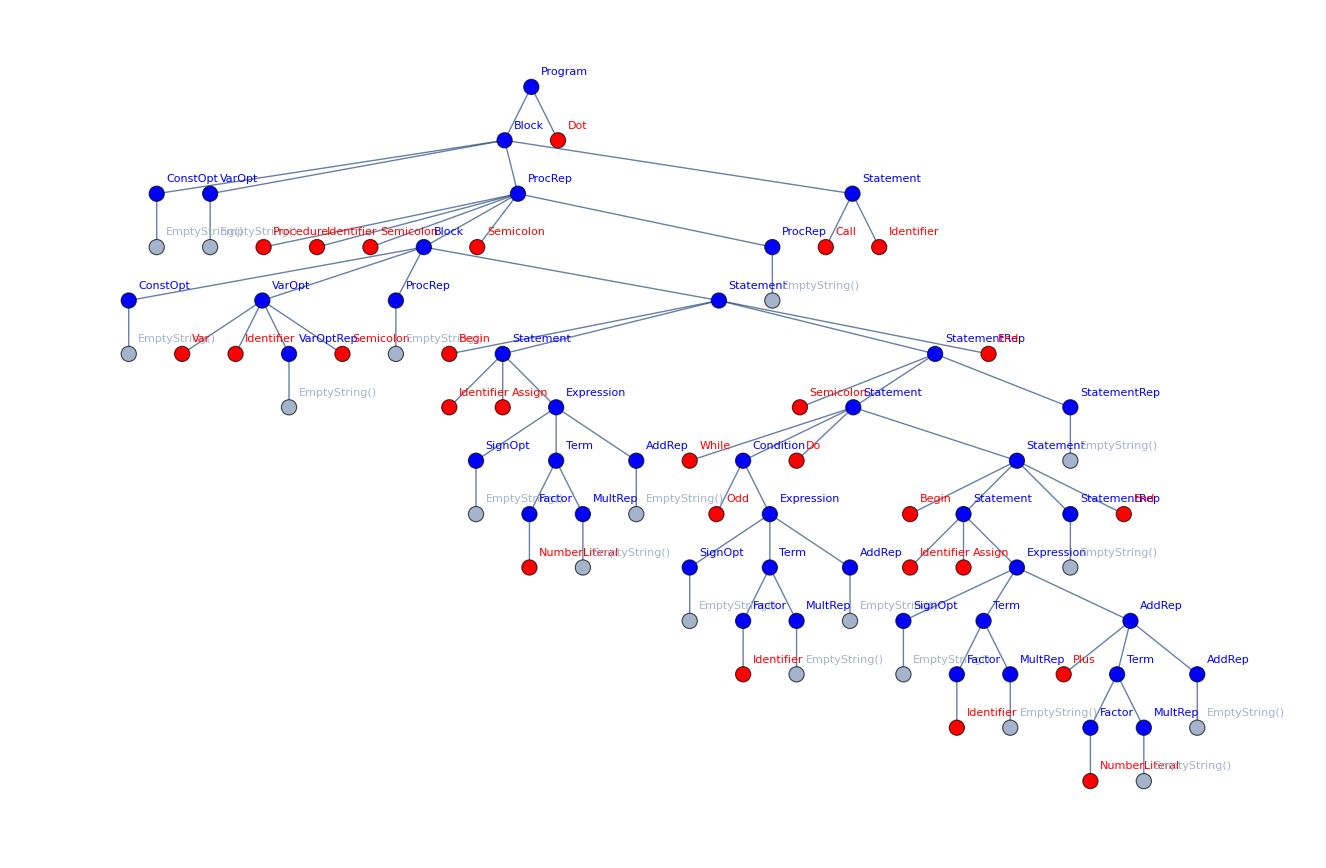

```mathematica
ParseTree[tokens]
```

```mathematica
CompilePL0ToASM[program]
```

Call <primes>
Return
Label <primes>
SetA 2
Store <primes::arg>
Label <primes::0::L1>
LoadA <primes::arg>
JumpOdd <primes::0::L2>
LoadA <primes::arg>
SetB 1
Add
Store <primes::$0>
LoadA <primes::$0>
Store <primes::arg>
Jump <primes::0::L1>
Label <primes::0::L2>
Return
Declare <primes::arg> 0
Declare <primes::$0> 0

```mathematica
Column[MachineInstructions[GetInstructions[CompilePL0ToASM[program]]]]
```

{Call,4}
{Return,0}
{SetA,2}
{Store,28}
{LoadA,28}
{JumpOdd,26}
{LoadA,28}
{SetB,1}
{Add,0}
{Store,29}
{LoadA,29}
{Store,28}
{Jump,8}
{Return,0}
0
0

## Algoritmos que aprenden

f(∑_i w_ij x_i + b_i)